```mathematica
caEvaluateCompiled=FunctionCompile[Function[{Typed[rule,TypeSpecifier["PackedArray"]["MachineInteger",1]],Typed[rad,"MachineInteger"],Typed[init,TypeSpecifier["PackedArray"]["MachineInteger",1]],Typed[eventCount,"Integer64"]},Module[{state,position,substate,rulePart,newCellValue},

state=init;
Do[
position=RandomInteger[{1,Length[state]}];
substate=state[[Mod[#,Length[state],1] & /@ Range[position-rad,position+rad]]];
rulePart=Fold[2#1+#2&,0,substate]+1;
newCellValue=rule[[rulePart]];
state[[position]]=newCellValue;
,eventCount];
state
]]];
```

Should be compiled for all machine targets:

```mathematica
caEvaluateCompiled=CompiledCodeFunction[…];
```

```mathematica
RandomAsynchronousCellularAutomaton[{rn_,2,r_},init_,{t_,ct_}]:=NestList[caEvaluateCompiled[Reverse[IntegerDigits[rn,2,2^(2r+1)]],r,#,ct]&,init,t]
```

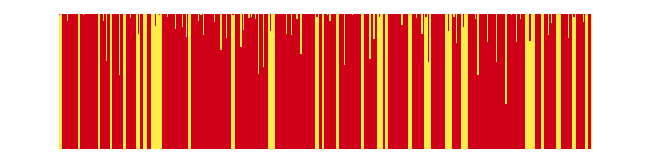

```mathematica
BlockRandom[SeedRandom[567];ArrayPlot[RandomAsynchronousCellularAutomaton[{232,2,1},RandomChoice[{.7,.3}->{1,0},400],{100,20}],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},MeshStyle->Orange,Frame->None]]
```